```mathematica
NEdistW[n_,p_,q_:1,x_,opts___]:=Module[{d,pr1,pr2,pr3,adn,func,st,v,rj,a,xr,prd},
Options[NEdistW] = {dist->1,prcm->300,prcpar->200,prcf->16,ad->0,function->1,stat->1};
d=dist/.{opts}/.Options[NEdistW];
func=function/.{opts}/.Options[NEdistW];
st=stat/.{opts}/.Options[NEdistW];
If[d==1||d==2||d==3,
If[st==1||st==2||st==3||st==4,
pr1=prcm/.{opts}/.Options[NEdistW];
pr2=prcf/.{opts}/.Options[NEdistW];
pr3=prcpar/.{opts}/.Options[NEdistW];
adn=ad/.{opts}/.Options[NEdistW];
v=IntModule[n,p,q,st,d,pr1,pr3,adn];
rj=If[st==1,Rj1[n,p],If[st==2,Rj1[n,{p,q-1}],If[st==3,Rj3[n,p],Rj4[n,p,q]]]];
g=If[st==1,g=Total[p],If[st==2,g=p+q-1,g=p]];
a=Table[(n-j)/n,{j,2,g}];
xr=Rationalize[x,0];
If[func==3,
prd=Product[a[[j]]^rj[[j]]*(a[[j]]-I*xr)^(-rj[[j]]),{j,1,g-1}];
If[d==2,SetPrecision[(v[[1]]*v[[4]]^v[[2]]*(v[[4]]-I*xr)^(-v[[2]])+(1-v[[1]])*v[[4]]^v[[3]]*(v[[4]]-I*xr)^(-v[[3]]))*prd,pr2],If[d==3,SetPrecision[(v[[1]]*v[[6]]^v[[3]]*(v[[6]]-I*xr)^(-v[[3]])+v[[2]]*v[[6]]^v[[4]]*(v[[6]]-I*xr)^(-v[[4]])+(1-v[[1]]-v[[2]])*v[[6]]^v[[5]]*(v[[6]]-I*xr)^(-v[[5]]))*prd,pr2],SetPrecision[v[[2]]^v[[1]]*(v[[2]]-I*xr)^(-v[[1]])*prd,pr2]]],
If[func==2,GNIG[r_,b_,l_,a_,w_]:=GNIGpdf[r,b,l,a,w],GNIG[r_,b_,l_,a_,w_]:=GNIGcdf[r,b,l,a,w]];
If[d==2,SetPrecision[v[[1]]*GNIG[rj,v[[2]],a,v[[4]],xr]+(1-v[[1]])*GNIG[rj,v[[3]],a,v[[4]],xr],pr2],If[d==3,SetPrecision[v[[1]]*GNIG[rj,v[[3]],a,v[[6]],xr]+v[[2]]*GNIG[rj,v[[4]],a,v[[6]],xr]+(1-v[[1]]-v[[2]])*GNIG[rj,v[[5]],a,v[[6]],xr],pr2],SetPrecision[GNIG[rj,v[[1]],a,v[[2]],xr],pr2]]]],
Print["Erroneous value for 'stat'"]],Print["Erroneous value for 'dist'"]]
]

IntModule[n_,p_,q_:1,st_,d_,pr1_:300,pr3_,adn_]:=Module[{},
mm=Table[SetPrecision[If[st==1,MomPhi21[n,p,h],If[st==2,MomPhi21[n,{p,q-1},h],If[st==3,MomPhi23[n,p,h],MomPhi24[n,p,q,h]]]],pr1],{h,1,2*d}];
If[d==1,Module1[mm],If[d==2,Module2[mm],Module3[mm,pr3,adn]]]
]

MomPhi21[n_,p_,h_]:=I^(-h)*D[Phi21[n,p,t],{t,h}]/.t->0
Phi21[n_,pk_,t_]:=Module[{},
p=Total[pk];
kstar=Floor[Count[pk,_?OddQ]/2];
(Gamma[(n-1)/2]*Gamma[n/2-1-n/2*I*t]/(Gamma[n/2-1]*Gamma[(n-1)/2-n/2*I*t]))^kstar
]

MomPhi23[n_,p_,h_]:=I^(-h)*D[Phi23[n,p,t],{t,h}]/.t->0
Phi23[n_,p_,t_]:=Product[Gamma[(n-1)/2+(j-1)/p]*Gamma[(n-1)/2-n/2*I*t]/(Gamma[(n-1)/2+(j-1)/p-n/2*I*t]*Gamma[(n-1)/2]),{j,1,p-Floor[p/2]}]*Product[Gamma[(n-1)/2+(j-1)/p]*Gamma[n/2-n/2*I*t]/(Gamma[(n-1)/2+(j-1)/p-n/2*I*t]*Gamma[n/2]),{j,1+p-Floor[p/2],p}]

MomPhi24[n_,p_,q_,h_]:=I^(-h)*D[Phi24[n,p,q,t],{t,h}]/.t->0
Phi24[n_,p_,q_,t_]:=Module[{aj,bjk,bjks,ap,bpk,bpks},
aj=Table[n-1,{j,1,Floor[p/2]}];
bjk=Table[Table[(k-2*j)/q,{k,1,q}],{j,1,Floor[p/2]}];
bjks=Floor[bjk];
ap=(n-1)/2;
bpk=Table[(2*k-p-1)/(2*q),{k,1,q}];
bpks=Floor[bpk];
Product[Product[Gamma[aj[[j]]+bjk[[j,k]]]*Gamma[aj[[j]]+bjks[[j,k]]-n*I*t]/(Gamma[aj[[j]]+bjks[[j,k]]]*Gamma[aj[[j]]+bjk[[j,k]]-n*I*t]),{k,1,q}],{j,1,Floor[p/2]}]*(Product[Gamma[ap+bpk[[k]]]*Gamma[ap+bpks[[k]]-n/2*I*t]/(Gamma[ap+bpks[[k]]]*Gamma[ap+bpk[[k]]-n/2*I*t]),{k,1,q}])^Mod[p,2]
]


Module1[mm_]:={mm[[1]]^2/(mm[[2]]-mm[[1]]^2),mm[[1]]/(mm[[2]]-mm[[1]]^2)}

Module2[mm_]:=Module[{p1,r1,r2,m},
Sort[Cases[{p1,r1,r2,m}/.NSolve[Table[mm[[h]]==MomMixGam[{p1},{r1,r2},{m,m},h],{h,1,4}],{p1,r1,r2,m}],{_Real,_Real,_Real,_Real}]][[2]]
]

Module3[mm_,prcpar_:200,ad_:0]:=Module[{vecn,p1,p2,r1,r2,r3,m},
vecn=Module2[mm];
{p1,p2,r1,r2,r3,m}/.FindRoot[Table[mm[[h]]==MomMixGam[{p1,p2},{r1,r2,r3},{m,m,m},h],{h,1,6}],{p1,vecn[[1]]},{p2,.99*(1-vecn[[1]])},{r1,vecn[[2]]},{r2,vecn[[3]]},{r3,ad+2*vecn[[3]]-vecn[[2]]},{m,vecn[[4]]},AccuracyGoal->prcpar]
]

MomMixGam[p_,r_,m_,h_]:=Module[{nt,ptot},
nt=Length[r];
ptot=Total[p];
(1-ptot)*Product[r[[nt]]+i,{i,0,h-1}]*m[[nt]]^(-h)+Sum[p[[j]]*Product[r[[j]]+i,{i,0,h-1}]*m[[j]]^(-h),{j,1,nt-1}]
]

Rj1[n_,pk_]:=Module[{hj,rj},
p=Total[pk];
hj=Table[Count[pk-(j-1),_?Positive],{j,1,p-2}]-1;
rj=Table[0,{j,1,p}];
rj[[3]]=hj[[1]]-kstar;rj[[4]]=hj[[2]]+kstar;
Do[rj[[j]]=rj[[j-2]]+hj[[j-2]],{j,5,p}];
Drop[rj,1]
]

Rj3[n_,p_]:=Table[Floor[(p-j+2)/2],{j,2,p}]

Rj4[n_,p_,q_]:=Module[{a,a1,a2,p2,q2},
a=Floor[(p-1)/q];a1=Floor[(q-1)/q*(p-1)/2];a2=Floor[(q-1)/q*(p+1)/2];
p2=Floor[p/2]; q2=Floor[q/2];
rj=Table[0,{j,1,p-1}];
Do[rj[[j]]=q2*((j-1)*q-2*Mod[q+1,2]*Floor[j/2]+Floor[(q+Mod[j,2])/2]),{j,1,a}];
rj[[a+1]]=-(p2-a*q2)^2+q*(p2-Floor[(a+1)/2])+Mod[q,2]*(a*p2+Mod[a,2]/4-a^2/4-a^2*q2);
Do[rj[[j]]=q*(p2-Floor[j/2]),{j,a+2,Min[p-2*a1,p-1]}];
Do[rj[[j]]=q*(p2-Floor[j/2]),{j,2+p-2*a1,2*p2-1,2}];
Do[rj[[j]]=q*(Floor[(p+1)/2]-Floor[j/2]),{j,1+p-2*a1,p-1,2}];
rj[[p-1-2*a1]]=rj[[p-1-2*a1]]+Mod[p,2]*(a2-a1)*(q-(p-1)/2+q*Floor[p/(2*q)]);
rj
]

GNIGpdf[r_,b_, l_,a_,w_] := Module[{g,P},
If[Count[r,_Integer]==Length[r] && And@@NonNegative[r] && And@@Positive[l],
g = Length[r];
c = Makec[r,l,g];
Product[l[[j]]^r[[j]], {j, 1, g}]*a^b*Sum[Exp[-l[[j]]*w]*Sum[c[[j]][[k]]*Gamma[k]/Gamma[k+b]*w^(k+b-1)*Hypergeometric1F1[b,k+b,-(a-l[[j]])*w],{k,1,r[[j]]}],{j, 1, g}]
 ] ]

GNIGcdf[r_,b_, l_,a_,w_] := Module[{g,P},
If[Count[r,_Integer]==Length[r] && And@@NonNegative[r] && And@@Positive[l],
g = Length[r];
c = Makec[r,l,g]; 
a^b*w^b/Gamma[b+1]*Hypergeometric1F1[b,b+1,-a*w]-Product[l[[j]]^r[[j]], {j, 1, g}]*a^b*Sum[Exp[-l[[j]]*w]*Sum[c[[j]][[k]]/l[[j]]^k*Gamma[k]*Sum[w^(b+i)*l[[j]]^i/Gamma[b+1+i]*Hypergeometric1F1[b,b+1+i,-(a-l[[j]])*w],{i,0,k-1}],{k,1,r[[j]]}],{j, 1, g}]
 ] ]

Makec[r_,l_,p_]:=Module[{c},
c=Table[Table[1,{j,1,Max[r]}],{i,1,p}];
Table[c=ReplacePart[c,(Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,1,i-1}]*Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,i+1,p}])/(r[[i]]-1)!,{i,r[[i]]}],{i,1,p}];
Table[Table[c=ReplacePart[c,Sum[((r[[i]]-k+j-1)!*(Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,1,i-1}]+Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,i+1,p}])*c[[i]][[r[[i]]-(k-j)]])/(r[[i]]-k-1)!,{j,1,k}]/k,{i,r[[i]]-k}],{k,1,r[[i]]-1}],{i,1,p}];
c
]
```

```mathematica
(*  Attention! Distributions are for the logarithms of the LRT statistics !  *)
```

```mathematica
(*  Example of use of module NEdistW  *)
```

```mathematica
(***  LRT for the test of independence of 3 groups of variables  ***)
```

```mathematica
(*  Example of the computation of a value of the near-exact c.d.f. (function->1, by default), which equates 2 exact moments (dist->1) for the negative logarithm of the l.r.t. statistic to test independence (stat->1) of 3 groups of variables, with 3, 4 and 5 variables, and a sample size of 25, at a point near the 0.95 quantile (that is, the point 45.11) *)
```

```mathematica
NEdistW[25,{3,4,5},,45.11,dist->1,stat->1]
```

0.9499941761058887

```mathematica
(*  Example of the computation of a value of the near-exact c.d.f. (function->1, by default), which equates 4 exact moments (dist->2) for the negative logarithm of the l.r.t. statistic to test independence (stat->1) of 3 groups of variables, with 3, 4 and 5 variables, and a sample size of 25, at a point near the 0.95 quantile (that is, the point 45.11) *)
```

```mathematica
NEdistW[25,{3,4,5},,45.11,dist->2,stat->1]
```

0.9499942171134919

```mathematica
(*  Example of the computation of a p-value for the near-exact c.d.f. (function->1, by default), which equates 2 exact moments (dist->1) for the negative logarithm of the l.r.t. statistic to test independence (stat->1) of 3 groups of variables, with 3, 4 and 5 variables, and a sample size of 25, corresponding to the computed value of the negative logarithm of the statistic equal to 47.9 *)
```

```mathematica
1-NEdistW[25,{3,4,5},,479/10,dist->1,stat->1]
```

0.024622897194004

```mathematica
(*  Computation of the .95 near-exact quantile for the negative logarithm of the l.r.t. statistic to test independence (stat->1) of 3 groups of variables, with 3, 4 and 5 variables, and a sample size of 25, for the near-exact c.d.f. (function->1), which equates 2 exact moments (dist->1)  *)
```

```mathematica
FindRoot[SetPrecision[NEdistW[25,{3,4,5},1,x,dist->1,stat->1,function->1],50]==95/100,{x,40},AccuracyGoal->30,WorkingPrecision->20]
```

{x→45.110479968850010962}

```mathematica
(*  Evaluation to 12 decimal places of the near-exact c.d.f. at the above .95 near-exact quantile  *)
```

```mathematica
SetPrecision[NEdistW[25,{3,4,5},1,45.110479969414586761,dist->1,stat->1,function->1],12]
```

0.950000000007

```mathematica
(*  Computation of the .99 near-exact quantile for the negative logarithm of the l.r.t. statistic to test independence (stat->1) of 3 groups of variables, with 3, 4 and 5 variables, and a sample size of 25, for the near-exact c.d.f. (function->1), which equates 2 exact moments (dist->1)  *)
```

```mathematica
FindRoot[SetPrecision[NEdistW[25,{3,4,5},1,x,dist->1,stat->1,function->1],50]==99/100,{x,40},AccuracyGoal->30,WorkingPrecision->20]
```

{x→51.15564080844967834}

```mathematica
(*  Evaluation to 12 decimal places of the near-exact c.d.f. at the above .99 near-exact quantile  *)
```

```mathematica
SetPrecision[NEdistW[25,{3,4,5},1,51.1556408084285332858508050822538257667`20.,dist->1,stat->1,function->1],12]
```

0.99

```mathematica
(*  Plot of the near-exact c.d.f. (function->1), which equates 2 exact moments (dist->1) for the negative logarithm of
 the l.r.t. statistic to test independence (stat->1) of 3 groups of variables, with 3, 4 and 5 variables, and a sample size of 25 *)
```

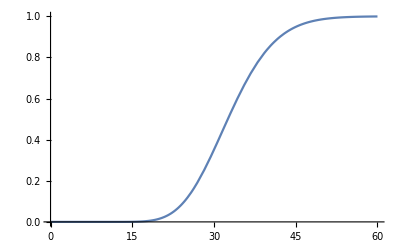

```mathematica
Plot[NEdistW[25,{3,4,5},1,x,dist->1,stat->1,function->1],{x,0,60},PlotRange->All]
```

```mathematica
(*  Plot of the near-exact p.d.f. (function->2),which equates 2 exact moments (dist->1) for the negative logarithm of
 the l.r.t. statistic to test independence (stat->1) of 3 groups of variables, with 3, 4 and 5 variables, and a sample size of 25 *)
```

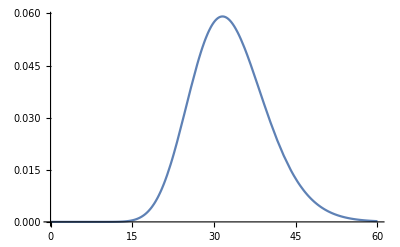

```mathematica
Plot[NEdistW[25,{3,4,5},1,x,dist->1,stat->1,function->2],{x,0,60}]
```

```mathematica
(*  Plot of the absolute value of the near-exact c.f. (function->3), which equates 2 exact moments (dist->1) for the negative logarithm of the l.r.t. statistic to test independence (stat->1) of 3 groups of variables, with 3, 4 and 5 variables, and a sample size of 25; and corresponding execution time *)
```

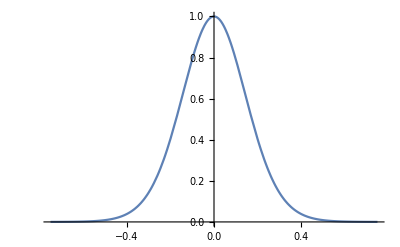

```mathematica
Plot[Abs[NEdistW[25,{3,4,5},,x,dist->1,stat->1,function->3]],{x,-.75,.75},PlotRange->All]
```

```mathematica
(*  Computation of a value of the near-exact c.f. (function->3), which equates 2 exact moments (dist->1), at the point 1/100, for the l.r.t. statistic to test independence (stat->1) of 3 groups of variables, with 3, 4 and 5 variables, and a sample size of 25; and corresponding execution time *)
```

```mathematica
NEdistW[25,{3,4,5},,.01,dist->1,stat->1,function->3]
```

0.943741456868469+0.323460266484519 ⅈ

```mathematica
(*  Example of the displayed error message when we give a wrong value for 'stat'  *)
```

```mathematica
NEdistW[25,{3,4,5},,23/10,dist->1,stat->-1]
```

Erroneous value for 'stat'

```mathematica
(*  Example of the displayed error message when we give a wrong value for 'dist'  *)
```

```mathematica
NEdistW[25,{3,4,5},,23/10,dist->0,stat->1]
```

Erroneous value for 'dist'

```mathematica
(***  LRT for the test of equality of 4 mean vectors  ***)
```

```mathematica
(*  Example of the computation of a value of the near-exact c.d.f. (function->1, by default), which equates 2 exact moments (dist->1, the default) for the negative logarithm of the l.r.t. statistic to test the equality of 4 mean vectors (stat->2) with an overall sample of size 20, at a point near the 0.05 quantile (that is, the point 5.05) *)
```

```mathematica
NEdistW[20,5,4,5.05,stat->2]
```

0.05002735570577804

```mathematica
(*  Example of the computation of a value of the near-exact c.d.f. (function->1, by default), which equates 4 exact moments (dist->2) for the negative logarithm of the l.r.t. statistic to test the equality of 4 mean vectors (stat->2) with an overall sample of size 20, at a point near the 0.05 quantile (that is, the point 5.05) *)
```

```mathematica
NEdistW[20,5,4,5.05,stat->2,dist->2]
```

0.05002853274061261

```mathematica
(*  Example of the computation of the near-exat p-value from a near-exact distribution that equates 4 exact moments (dist->2) for the negative logarithm of the l.r.t. statistic to test the equality of 4 mean vectors (stat->2) with an overall sample of size 20, at a point near the 0.05 quantile (that is, the point 5.05) *)
```

```mathematica
1-NEdistW[20,5,4,5.05,stat->2,dist->2]
```

0.94997146725938739

```mathematica
(*  Computation of the .05 near-exact quantile for the negative logarithm of the l.r.t. statistic to test the equality of 4 mean vectors of dimension 5 (stat->2), for the near-exact c.d.f. (function->1), which equates 4 exact moments (dist->2)  *)
```

```mathematica
FindRoot[SetPrecision[NEdistW[20,5,4,x,dist->2,stat->2],50]==5/100,{x,5},AccuracyGoal->30,WorkingPrecision->20]
```

{x→5.0493562876604916366}

```mathematica
(*  Evaluation to 12 decimal places of the near-exact c.d.f. at the above .05 near-exact quantile  *)
```

```mathematica
SetPrecision[NEdistW[20,5,4,5.04935628766049163662601314405805011022`20.,dist->2,stat->2],15]
```

0.0500000000000003